```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/shi/file/git/Critical-region/QCD/v1

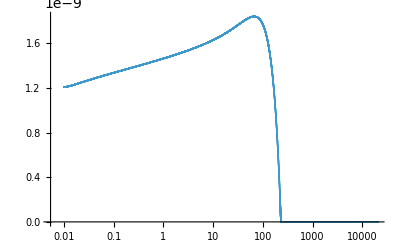

```mathematica
k=Flatten[Import["./Tc/BUFFER/K.DAT"]];
rho=Flatten[Import["./Tc/BUFFER/RHO.DAT"]];
ListPlot[Transpose[{k,rho[[1;;Length[k]]]/(142.5841442k)}],ScalingFunctions->{"Log",Automatic},PlotRange->{All,All}]
```